```mathematica
(* List of fast Deleglise-Rivat alpha factors for x ≤ 10^24 found by running pi(x) benchmarks using the find_fastest_alpha.sh script *)

alphaDelegliseRivat =  { (* {x, alpha} *) {1, 1}, {10^1, 1}, {10^2, 1},{10^3, 1},{10^4, 1.095},{10^5, 1.174},{10^6,1.310}, {10^7,1.591},{10^8,2.095},{10^9,3.178},{10^10,3.795},{10^11,4.779}, {10^12,6.103}, {10^13, 7.810},  {10^14, 10.545}, {10^15,  13.969}, {10^16, 17.461}, {10^17,20.862}, {10^18,24.146}, {10^19, 28.184},{10^20, 33.230},{10^21,38.64}, {10^22,44.296}, {10^23, 50.845},{10^24,57.647} }
```

{{1,1},{10,1},{100,1},{1000,1},{10000,1.095},{100000,1.174},{1000000,1.31},{10000000,1.591},{100000000,2.095},{1000000000,3.178},{10000000000,3.795},{100000000000,4.779},{1000000000000,6.103},{10000000000000,7.81},{100000000000000,10.545},{1000000000000000,13.969},{10000000000000000,17.461},{100000000000000000,20.862},{1000000000000000000,24.146},{10000000000000000000,28.184},{100000000000000000000,33.23},{1000000000000000000000,38.64},{10000000000000000000000,44.296},{100000000000000000000000,50.845},{1000000000000000000000000,57.647}}

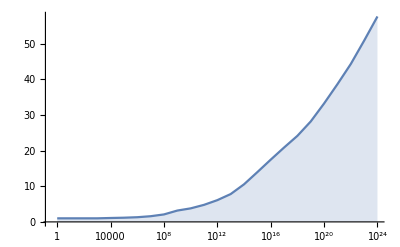

```mathematica
ListLogLinearPlot[alphaDelegliseRivat,Filling->Bottom, Joined-> True]
```

```mathematica
(* alpha is a tuning factor that balances the compuation of the easy special leaves and the hard special leaves. The formula below is used in the file src/primecount.cpp to calculate a fast alpha factor for the computation of pi(x). *)

NonlinearModelFit[alphaDelegliseRivat, a(Log[x])^3 + b (Log[x])^2 + c Log[x] + d, {a,b, c, d}, x]
```

FittedModel[1.3724-0.110407 Log[x]+0.0018113 Log[x]^2+0.00033826 Log[x]^3]

```mathematica
(* List of fast Lagarias-Miller-Odlyzko alpha factors found by running pi(x) benchmarks. *)

alphaLMO = {(* {x, alpha} *) {1, 1},{10^10, 1.208}, {10^11, 1.281},  {10^12, 1.364},{10^13, 1.679},{10^14, 1.890},{10^15,2.011},{10^16, 2.113},{10^17, 2.359},{10^18, 2.556}}
```

{{1,1},{10000000000,1.208},{100000000000,1.281},{1000000000000,1.364},{10000000000000,1.679},{100000000000000,1.89},{1000000000000000,2.011},{10000000000000000,2.113},{100000000000000000,2.359},{1000000000000000000,2.556}}

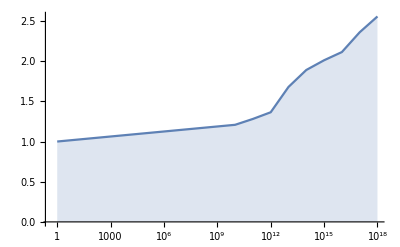

```mathematica
ListLogLinearPlot[alphaLMO,Filling->Bottom, Joined-> True]
```

```mathematica
(* alpha is a tuning factor that balances the compuation of the easy special leaves and the hard special leaves. The formula below is used in the file src/primecount.cpp to calculate a fast alpha factor for the computation of pi(x). *)
```

```mathematica
NonlinearModelFit[alphaLMO, a(Log[x])^2 + b  Log[x] + c, {a,b, c}, x]
```

FittedModel[0.990948-0.0261411 Log[x]+0.00156512 Log[x]^2]